```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
dat0=Flatten[Import["output.dat"]];
dos=Flatten[Import["dos.dat"]];
```

C:\Users\Brad\Documents\Visual Studio 2017\Projects\ConsoleApplication1\ConsoleApplication1

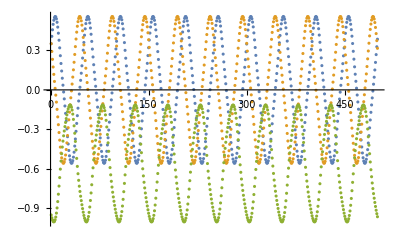

```mathematica
n=627;
point = 1;
datx=Take[dat0,{point,Length[dat0],n*3}];
daty=Take[dat0,{n+point,Length[dat0],n*3}];
datz=Take[dat0,{2n+point,Length[dat0],n*3}];
ListPlot[{datx,daty,datz},PlotRange->All]
```

```mathematica
ℏ=1.05*10^-34;
e=1.6*10^-19;
m0=9.1*10^-31;
kB=1.38*10^-23;
jtoev=6.242*10^18;
c=13.2/2;
a =5.3/Sqrt[2];

v [f_]:=(9.1*10^-31)10^-20/(10^-12)*1/ℏ{D[f,kx],D[f,ky],D[f,kz]};
kf[F_]:=Sqrt[(F 2Pi (e/(1.6*10^-19))/(ℏ/(9.1*10^-31)*10^20) (1/10^-12))/Pi];
ty= 1.6*10^-22 * 1/(9.1*10^-31) 1/(10^-10)^2 10^-24;

cdevs=5;
tdevs=500;
θmax=100;
θmin=0;
θdevs=20;
Bfield=45.*1.6*10^-19 * 10^-12/(9.1*10^-31);
angles = Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}];
phis = {0.*Pi/180,15*Pi/180.,30.*Pi/180,45.*Pi/180};


ϵ01[kx_,ky_,kz_,t_]:=   500t-500 2t (Cos[kx a]+Cos[ky a ])-+2 t*.01Cos[kz c/2]
energy=ϵ01[kx,ky,kz,ty];
velocity01=Simplify[v[energy]];
velocityz01=velocity01[[3]];
kf001 = FindRoot[ϵ01[0,ky,0,ty]==0,{ky,.8}][[1,2]];
velz01[kx_,ky_,kz_]=velocityz01;

num=24;
phi1=Table[{ArcTan[8.i/num],Sqrt[(i)^2.+(num/8)^2]},{i,0,num/8}];
phi2=Transpose[{Pi/2-Reverse[phi1[[All,1]]],Reverse[phi1[[All,2]]]}];
phi3=Transpose[{Pi-Reverse[phi2[[All,1]]],phi1[[All,2]]}];
phi4=Transpose[{3Pi/2-Reverse[phi3[[All,1]]],Reverse[phi1[[All,2]]]}];
phi5=Transpose[{4Pi/2-Reverse[phi4[[All,1]]],phi1[[All,2]]}];
phi6=Transpose[{5Pi/2-Reverse[phi5[[All,1]]],phi1[[All,2]]//Reverse}];
phi7=Transpose[{6Pi/2-Reverse[phi6[[All,1]]],phi1[[All,2]]}];
phi8=Transpose[{7Pi/2-Reverse[phi7[[All,1]]],phi1[[All,2]]//Reverse}];phispecial=((Join[phi1,phi2,phi3,phi4,phi5,phi6,phi7,phi8])[[All,1]]//DeleteDuplicates)+Pi/4;
start01=Flatten[Table[Table[{FindRoot[(energy/.kx->r Cos[θ]/.ky->r Sin[θ])==0,{r,.8 }][[1,2]]Cos[θ],FindRoot[(energy/.kx->r Cos[θ]/.ky->r Sin[θ])==0,{r,.8 }][[1,2]]Sin[θ],kz},{θ,phispecial}],{kz,-2Pi/c,2Pi/c,4.Pi/c /cdevs}],1];

phi=50*Pi/180;
theta=80*Pi/180;
phi=25*Pi/180;
theta=40*Pi/180;
B = {Bfield*Sin[theta]Cos[phi],Bfield*Sin[theta]Sin[phi],Bfield*Cos[theta]};


fx[t_,kx_,ky_,kz_]=-1./(11538.5)Cross[velocity01,B][[1]];
fy[t_,kx_,ky_,kz_]=-1./(11538.5)Cross[velocity01,B][[2]];
fz[t_,kx_,ky_,kz_]=-1./(11538.5)Cross[velocity01,B][[3]];
```

```mathematica
Export["starts.dat",Flatten[start01,1]]
```

starts.dat

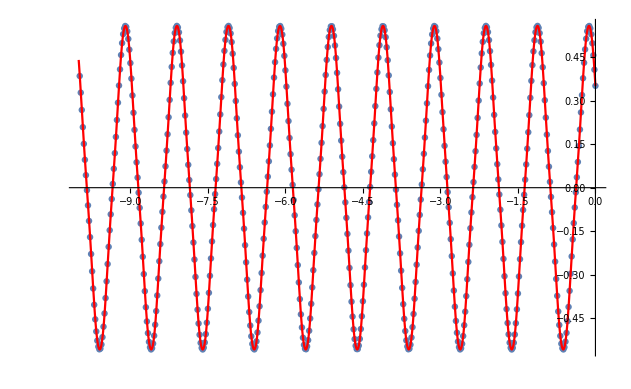

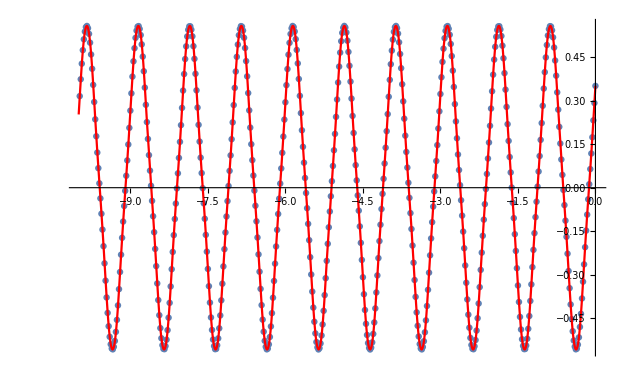

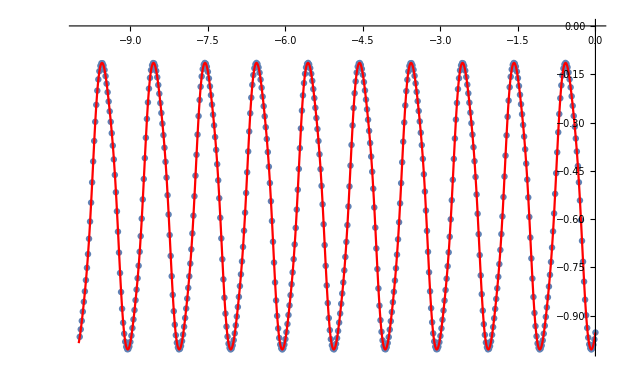

```mathematica
solve2=NDSolve[{kx'[t]==fx[t,kx[t],ky[t],kz[t]],ky'[t]==fy[t,kx[t],ky[t],kz[t]],kz'[t]==fz[t,kx[t],ky[t],kz[t]],kx[0]==start01[[1,1]],ky[0]==start01[[1,2]],kz[0]==start01[[1,3]]},{kx[t],ky[t],kz[t]},{t,-10,0}];
Show[ListPlot[Transpose[{10/Length[datx]*(-Range[Length[datx]]+1),datx}],PlotRange->All],Plot[solve2[[1,1,2]],{t,-10,0},PlotStyle->Red]]
Show[ListPlot[Transpose[{10/Length[daty]*(-Range[Length[datx]]+1),daty}],PlotRange->All],Plot[solve2[[1,2,2]],{t,-10,0},PlotStyle->Red]]
Show[ListPlot[Transpose[{10/Length[datz]*(-Range[Length[datx]]+1),datz}],PlotRange->All],Plot[solve2[[1,3,2]],{t,-10,0},PlotStyle->Red]]
```

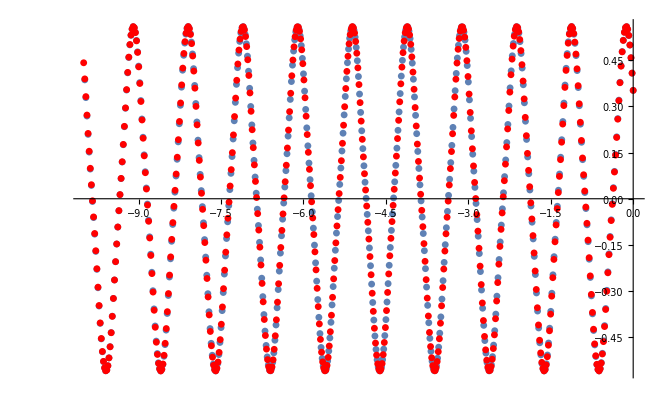

```mathematica
tnum = 100;
τ=0.1;τt=tnum*τ;τs=tnum*τ/tdevs;times=Range[-tnum*τ,0,tnum*τ/(tdevs-1)];
Show[ListPlot[Transpose[{10/Length[datx]*(-Range[Length[datx]]+1),datx}],PlotRange->All],ListPlot[Transpose[{times,solve2[[1,1,2]]/.t->times}],PlotStyle->Red]]
```

```mathematica
dos2=1/((velocity01[[1]]/.kx->#[[1]]/.ky->#[[2]]/.kz->#[[3]])^2+(velocity01[[2]]/.kx->#[[1]]/.ky->#[[2]]/.kz->#[[3]])^2+(velocity01[[3]]/.kx->#[[1]]/.ky->#[[2]]/.kz->#[[3]])^2)^.5&/@start01;
```

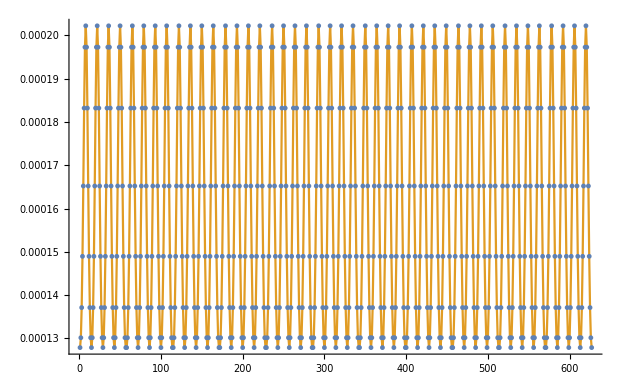

```mathematica
ListPlot[{dos,dos2},Joined->{False,True}]
```

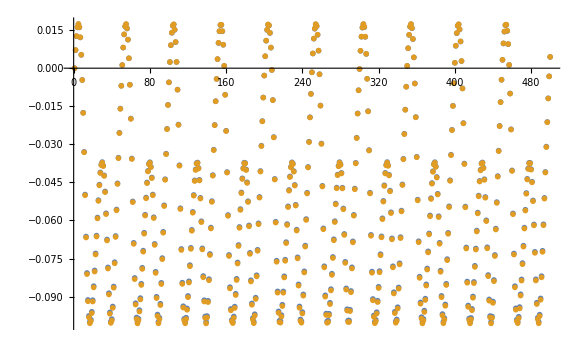

```mathematica
vzdatC=velocity01[[3]]/.kz->datz;
pointNumber=627;
datz0=Flatten[Import["outputVz.dat"]];
vzdat=Take[datz0,{pointNumber,Length[datz0],n}];
ListLinePlot[{vzdat,vzdatC},PlotRange->All,Joined->{False,False}]
```

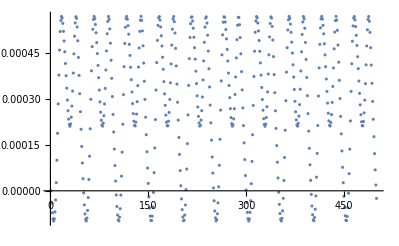

```mathematica
ListPlot[vzdat-vzdatC]
```

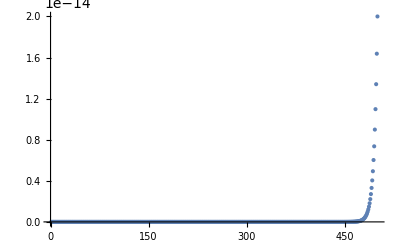

```mathematica
ListPlot[times1,PlotRange->All]
```

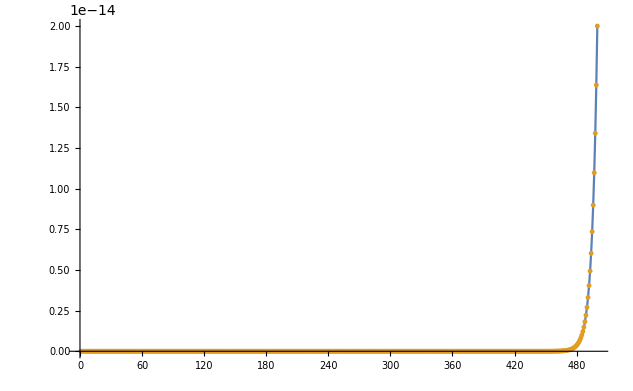

```mathematica
times1=Flatten[Import["times.dat"]];
time=Exp[Sort[-(Range[500]-1)]*10/500/.1]*10^-12 * 10/500.;
ListPlot[{times1,time},Joined->{True,False},PlotRange->All]
```

```mathematica
times1[[500]]
time[[500]]
```

2.×10^-14

2.×10^-14

```mathematica
times1[[1]]^2
```

8.25812×10^-115

```mathematica
For[i=1,i≤500,i++, soln2=NDSolve[{kx'[t]==fx[t,kx[t],ky[t],kz[t]],ky'[t]==fy[t,kx[t],ky[t],kz[t]],kz'[t]==fz[t,kx[t],ky[t],kz[t]],kx[0]==start01[[i,1]],ky[0]==start01[[i,2]],kz[0]==start01[[i,3]]},{kx[t],ky[t],kz[t]},{t,0,10}];
out={soln2[[1,1,2]]/.t->10./500*Range[500],soln2[[1,2,2]]/.t->10./500*Range[500],soln2[[1,3,2]]/.t->10./500*Range[500]};
]//Timing
```

{4.10938,Null}

```mathematica
cond=Flatten[Import["conductivity.dat"],1];
ListLinePlot[1/cond]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-